```mathematica
coords[{x_,y_,z_}]:={x/2+y,x Tan[Pi/3]/2};
```

```mathematica
xlist={};
```

```mathematica
For[n=40;i=1,i≤n,i++,
For[j=1;x=i/n,j<n-i,j++,y=j/n;z=1-x-y;xlist=Append[xlist,{x,y,z}]]]
```

```mathematica
xlist;
```

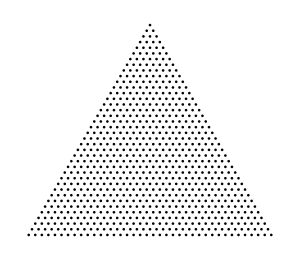

```mathematica
Graphics[Disk[coords[#],.005]&/@xlist,ImageSize->300]
```

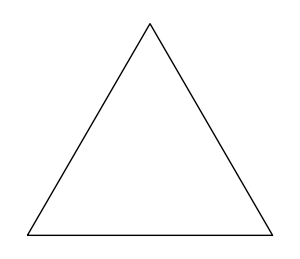

```mathematica
frame=Graphics[{Thick,Line[{{0,0},{1,0},{0.5,Sqrt[3]/2},{0,0}}]},ImageSize->300]
```

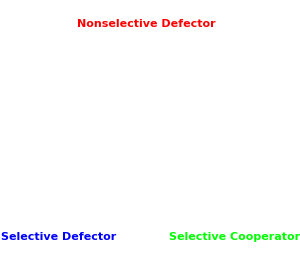

```mathematica
vertices=Graphics[{Text[Style["Selective Defector",Blue,Medium,Bold],{0-0.02,0-0.02}],Text[Style["Selective Cooperator",Green,Medium,Bold],{1+0.02,0-0.02}],Text[Style["Nonselective Defector",Red,Medium,Bold],{0.5,√3/2+0.02}]},ImageSize->300]
```

```mathematica
ulist={};
```

```mathematica
ulist2={};
```

```mathematica
For[i=1,i≤Length[xlist],i++,
uvector={u2,u3,u4}/.Last[Solve[seqns/.{x1->0,x2->xlist[[i]][[1]],x3->xlist[[i]][[2]],x4->xlist[[i]][[3]],q->.1}, {s1,s2,s3,s4}]]/.rstp1/.{c->1,q->.1};
ulist=Append[ulist,uvector]]
```

```mathematica
For[i=1,i≤Length[xlist],i++,
uvector={u2,u3,u4}/.Last[Solve[seqns/.{x1->0,x2->xlist[[i]][[1]],x3->xlist[[i]][[2]],x4->xlist[[i]][[3]],q->.1}, {s1,s2,s3,s4}]]/.rstp1/.{c->.5,q->.1};
ulist2=Append[ulist2,uvector]]
```

```mathematica
ulist;
```

```mathematica
ubarlist=Total[Transpose[ulist*xlist]];
```

```mathematica
ubarlist2=Total[Transpose[ulist2*xlist]];
```

```mathematica
gradient3d=xlist*(ulist-ubarlist);
```

```mathematica
gradient3d2=xlist*(ulist2-ubarlist2);
```

```mathematica
simdata=coords[#]& /@xlist;
```

```mathematica
simvector=coords[#]& /@gradient3d;
```

```mathematica
simvector2=coords[#]& /@gradient3d2;
```

```mathematica
vector={};
```

```mathematica
vector2={};
```

```mathematica
For[i=1,i≤Length[simdata],i++,vector=Append[vector,{simdata[[i]],simvector[[i]]}]]
```

```mathematica
For[i=1,i≤Length[simdata],i++,vector2=Append[vector2,{simdata[[i]],simvector2[[i]]}]]
```

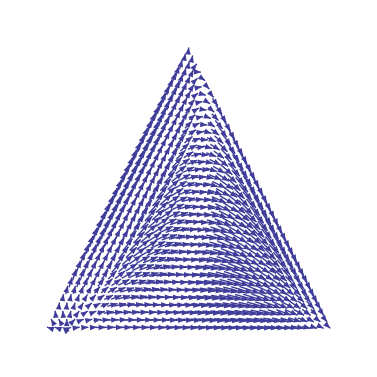

```mathematica
vectorfield=ListVectorPlot[vector,VectorPoints->simdata,Frame->False]
```

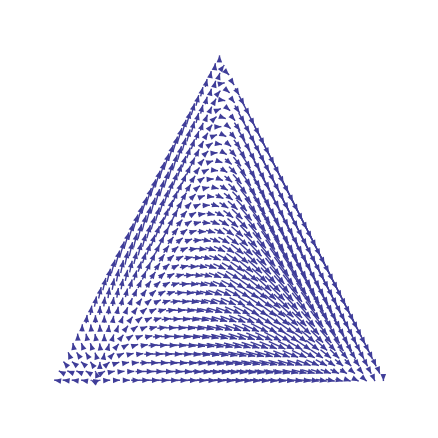

```mathematica
vectorfield2=ListVectorPlot[vector2,VectorPoints->simdata,Frame->False]
```

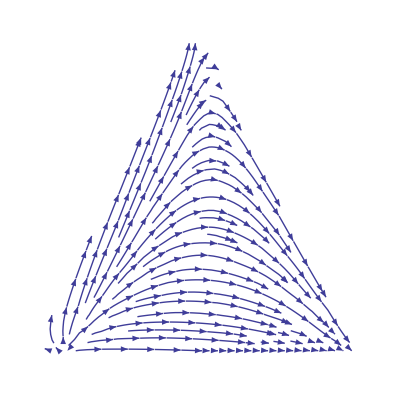

```mathematica
ListStreamPlot[vector,StreamPoints->simdata,Frame->False,RegionFunction->Function[{x,y},Sqrt[3]*x+y<Sqrt[3] && y<Sqrt[3]*x]]
```

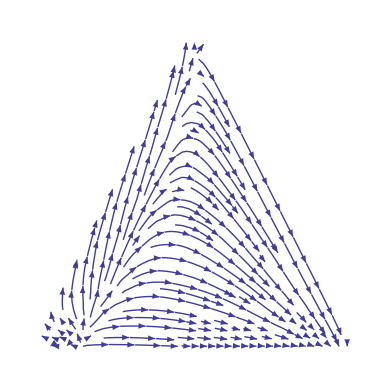

```mathematica
streamplot2=ListStreamPlot[vector2,StreamPoints->simdata,Frame->False,RegionFunction->Function[{x,y},Sqrt[3]*x+y<Sqrt[3] && y<Sqrt[3]*x]]
```

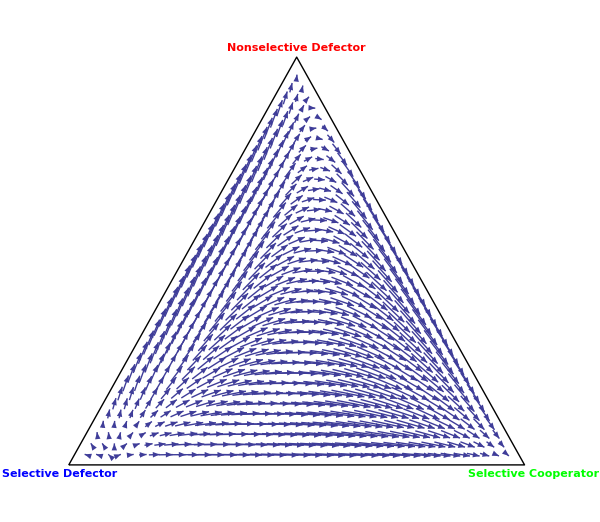

```mathematica
Show[frame,vertices,vectorfield, ImageSize->600]
```